```mathematica
x1=1;h=0.04;n=24;
```

```mathematica
Array[xdata,n,0];Array[ydata,n,0];
```

```mathematica
ydata[0]=1.01;
```

```mathematica
ydata[1]=0.915311;
```

```mathematica
ydata[2]=0.865912;
```

```mathematica
ydata[3]=0.78922;
```

```mathematica
ydata[4]=0.750595;
```

```mathematica
ydata[5]=0.6875;
```

```mathematica
ydata[6]=0.656868;
```

```mathematica
ydata[7]=0.604248;
```

```mathematica
ydata[8]=0.57966;
```

```mathematica
ydata[9]=0.535251;
```

```mathematica
ydata[10]=0.515306;
```

```mathematica
ydata[11]=0.477431;
```

```mathematica
ydata[12]=0.461103;
```

```mathematica
ydata[13]=0.428497;
```

```mathematica
ydata[14]=0.415023;
```

```mathematica
ydata[15]=0.386719;
```

```mathematica
ydata[16]=0.375521;
```

```mathematica
ydata[17]=0.350765;
```

```mathematica
ydata[18]=0.341401;
```

```mathematica
ydata[19]=0.319602;
```

```mathematica
ydata[20]=0.311728;
```

```mathematica
ydata[21]=0.292415;
```

```mathematica
ydata[22]=0.285763;
```

```mathematica
ydata[23]=0.268555;
```

```mathematica
ydata[24]=0.262911;
```

```mathematica
For[i=0,i<=n,i++,
xdata[i]=x1+h*i;];
```

```mathematica
MatrixForm[Table[{xdata[i],ydata[i]},{i,0,n}]]
```

(1. | 1.01
1.04 | 0.915311
1.08 | 0.865912
1.12 | 0.78922
1.16 | 0.750595
1.2 | 0.6875
1.24 | 0.656868
1.28 | 0.604248
1.32 | 0.57966
1.36 | 0.535251
1.4 | 0.515306
1.44 | 0.477431
1.48 | 0.461103
1.52 | 0.428497
1.56 | 0.415023
1.6 | 0.386719
1.64 | 0.375521
1.68 | 0.350765
1.72 | 0.341401
1.76 | 0.319602
1.8 | 0.311728
1.84 | 0.292415
1.88 | 0.285763
1.92 | 0.268555
1.96 | 0.262911)

```mathematica
data25=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}];
```

```mathematica
inpln25:=InterpolatingPolynomial[data25,x];
```

```mathematica
Collect[inpln25,x]
```

3.35989×10^18-5.67593×10^19 x+4.58586×10^20 x^2-2.35829×10^21 x^3+8.66608×10^21 x^4-2.42182×10^22 x^5+5.34814×10^22 x^6-9.5727×10^22 x^7+1.41337×10^23 x^8-1.74261×10^23 x^9+1.80954×10^23 x^10-1.59145×10^23 x^11+1.18921×10^23 x^12-7.55829×10^22 x^13+4.08166×10^22 x^14-1.8669×10^22 x^15+7.19197×10^21 x^16-2.31381×10^21 x^17+6.14086×10^20 x^18-1.32112×10^20 x^19+2.24618×10^19 x^20-2.90466×10^18 x^21+2.68445×10^17 x^22-1.57934×10^16 x^23+4.4447×10^14 x^24

```mathematica
inplnPlot:=Plot[inpln25,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

```mathematica
pointsPlot:=ListPlot[data25,PlotStyle->Red, PlotLegends->"начальное значение"];
```

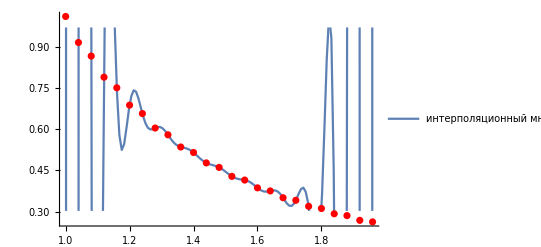

```mathematica
Show[{inplnPlot,pointsPlot}]
```

```mathematica
data12=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,2}];
inpln12:=InterpolatingPolynomial[data12,x];Collect[inpln12,x]
```

374.044-3074.09 x+11774.3 x^2-27453.3 x^3+43213.9 x^4-48288. x^5+39238.8 x^6-23350.7 x^7+10096.6 x^8-3092.86 x^9+637.046 x^10-79.2108 x^11+4.49619 x^12

```mathematica
inplnPlot12:=Plot[inpln12,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

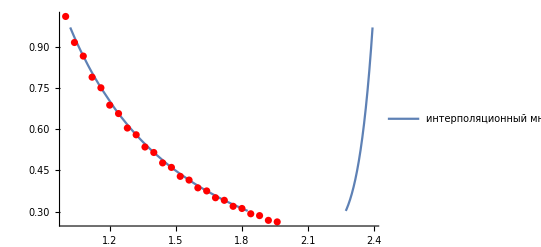

```mathematica
Show[{inplnPlot12,pointsPlot}]
```

```mathematica
data8=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,3}];
```

```mathematica
inpln8:=InterpolatingPolynomial[data8,x];Collect[inpln8,x]
```

13757.3-77754.6 x+190913. x^2-265968. x^3+229962. x^4-126375. x^5+43112.1 x^6-8348.53 x^7+702.695 x^8

```mathematica
inplnPlot8:=Plot[inpln8,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

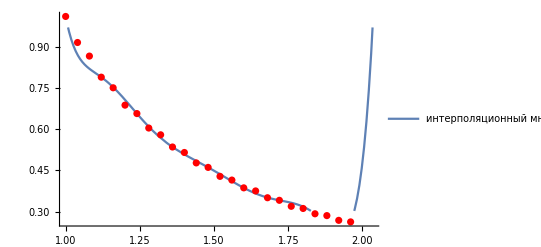

```mathematica
Show[{inplnPlot8,pointsPlot}]
```

```mathematica
data5=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,6}];
```

```mathematica
inpln5:=InterpolatingPolynomial[data5,x];Collect[inpln5,x]
```

7.81567-14.6379 x+11.4027 x^2-4.15386 x^3+0.583388 x^4

```mathematica
inplnPlot5:=Plot[inpln5,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
```

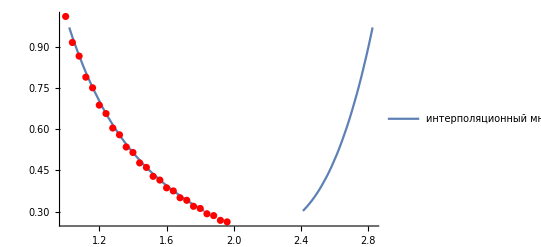

```mathematica
Show[{inplnPlot5,pointsPlot}]
```

```mathematica
spln25:=Interpolation[data25,Method->"Spline"];
```

```mathematica
splnPlot25:=Plot[{spln25[x]},{x,xdata[0]-h,xdata[n]+h},PlotLegends->{"сплайн"},PlotStyle->Green,PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}]
```

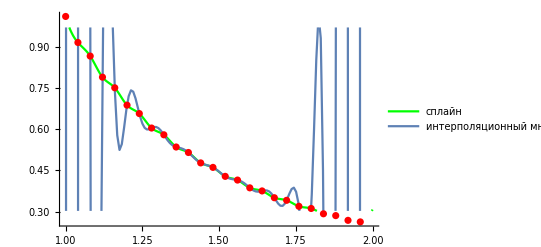

```mathematica
Show[{splnPlot25,inplnPlot,pointsPlot}]
```

```mathematica
spln12:=Interpolation[data12,Method->"Spline"];
```

```mathematica
splnPlot12:=Plot[{spln12[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

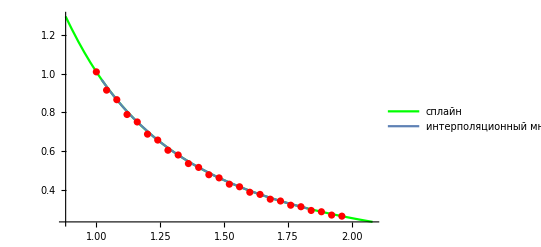

```mathematica
Show[{splnPlot12,inplnPlot12,pointsPlot}]
```

```mathematica
spln8:=Interpolation[data8,Method->"Spline"];
```

```mathematica
splnPlot8:=Plot[{spln8[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

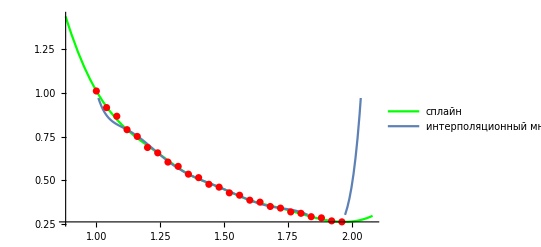

```mathematica
Show[{splnPlot8,inplnPlot8,pointsPlot}]
```

```mathematica
spln5:=Interpolation[data5,Method->"Spline"];
```

```mathematica
splnPlot5:=Plot[{spln5[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
```

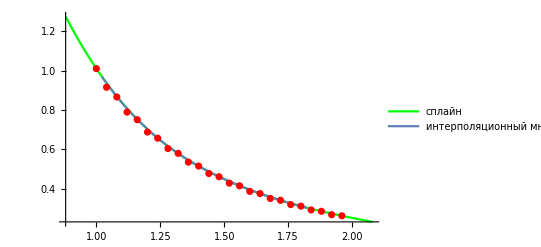

```mathematica
Show[{splnPlot5,inplnPlot5,pointsPlot}]
```

```mathematica
Clear[a,b]
```

```mathematica
rules1=FindFit[data25,a+b*x,{a,b},x];
```

```mathematica
y1=a+b*x/.rules1
f1[x_]:=a+b*x/.rules1;
```

1.57171-0.713658 x

```mathematica
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
```

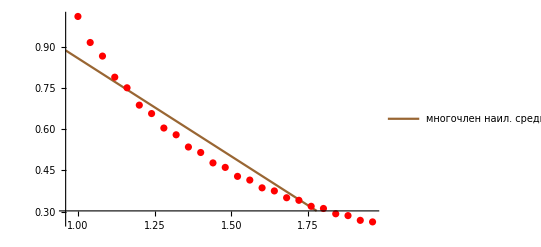

0.0828802

```mathematica
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
Clear[a,b]
```

3.15114-2.9323 x+0.749542 x^2

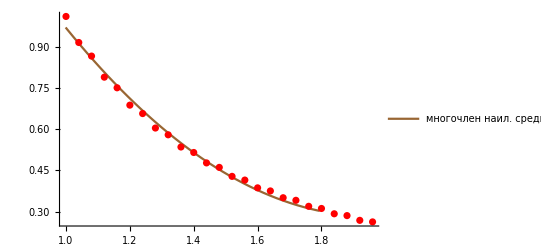

0.00547398

```mathematica
rules1=FindFit[data25,a+b*x+c*x*x,{a,b,c},x];
y1=a+b*x+c*x*x/.rules1
f1[x_]:=a+b*x+c*x*x/.rules1;
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
∑_(i=0)^(n-1) ydata[i]*(xdata[i+1]-xdata[i])
∑_(i=1)^n ydata[i]*(xdata[i]-xdata[i-1])
∑_(i=0)^(n-1) (ydata[i]+ydata[i+1])/2(xdata[i+1]-xdata[i])
h/3*(ydata[0]+ydata[n]+4*∑_(i=1)^(n/2) ydata[2*i-1]+2*∑_(i=1)^(n/2-1) ydata[2*i])
```

0.504976

0.475092

0.490034

0.48817